Plot3D::cfun: Value of option ColorFunction -> Vista is not a valid color function, or a gradient ColorData entity.

-Graphics3D-

-Graphics3D-

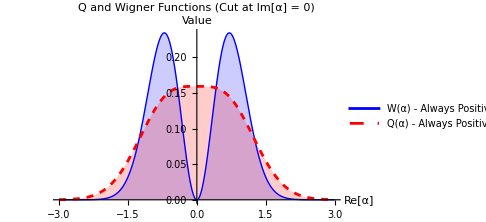

```mathematica
(*Definition of phase space coordinates*)r2[x_,y_]:=x^2+y^2

(*--------------------------------------------------------*)
(*1. Q function (Husimi) for statistical mixture (1/2) (|0⟩⟨0|+ |1⟩⟨1|)*)
(*Q_M(α)=1/(2π)*(1+ |α|^2)*Exp[-|α|^2]*)

QFunctionMixed01[x_,y_]:=(1/(2*Pi))*(1+r2[x,y])*Exp[-r2[x,y]]

(*--------------------------------------------------------*)
(*2. Wigner function for statistical mixture (1/2) (|0⟩⟨0|+ |1⟩⟨1|)*)
(*W_M(α)=4/π* |α|^2*Exp[-2|α|^2]*)

WignerFunctionMixed01[x_,y_]:=(4/Pi)*r2[x,y]*Exp[-2*r2[x,y]]

(*--------------------------------------------------------*)
(*a) Plot Q function*)

Plot3D[QFunctionMixed01[x,y],{x,-3,3},{y,-3,3},PlotRange->All,ColorFunction->"Vista",Mesh->None,AxesLabel->{"Re[α] (X1)","Im[α] (X2)","Q(α)"},PlotLabel->Style["Q Function for Mixed State (|0⟩⟨0| + |1⟩⟨1|)/2",Bold,14],BoxRatios->{1,1,0.5},ImageSize->Large]

(*--------------------------------------------------------*)
(*b) Plot Wigner function-should always be positive*)

Plot3D[WignerFunctionMixed01[x,y],{x,-3,3},{y,-3,3},PlotRange->All,ColorFunction->"Rainbow",Mesh->None,AxesLabel->{"Re[α] (X1)","Im[α] (X2)","W(α)"},PlotLabel->Style["Wigner Function for Mixed State (Always Positive/Classical-like)",Bold,14,Blue],BoxRatios->{1,1,0.5},ImageSize->Large]

(*--------------------------------------------------------*)
(*c) 2D slice to display values and compare Q and W*)

Plot[{WignerFunctionMixed01[x,0],QFunctionMixed01[x,0]},{x,-3,3},PlotLabel->Style["Q and Wigner Functions (Cut at Im[α] = 0)",Bold,14],PlotLegends->{"W(α) - Always Positive","Q(α) - Always Positive"},AxesLabel->{"Re[α]","Value"},GridLines->{None,{0}},PlotStyle->{Directive[Thick,Blue],Directive[Dashed,Red]},Filling->{1->Axis,2->Axis},ImageSize->Medium]
```